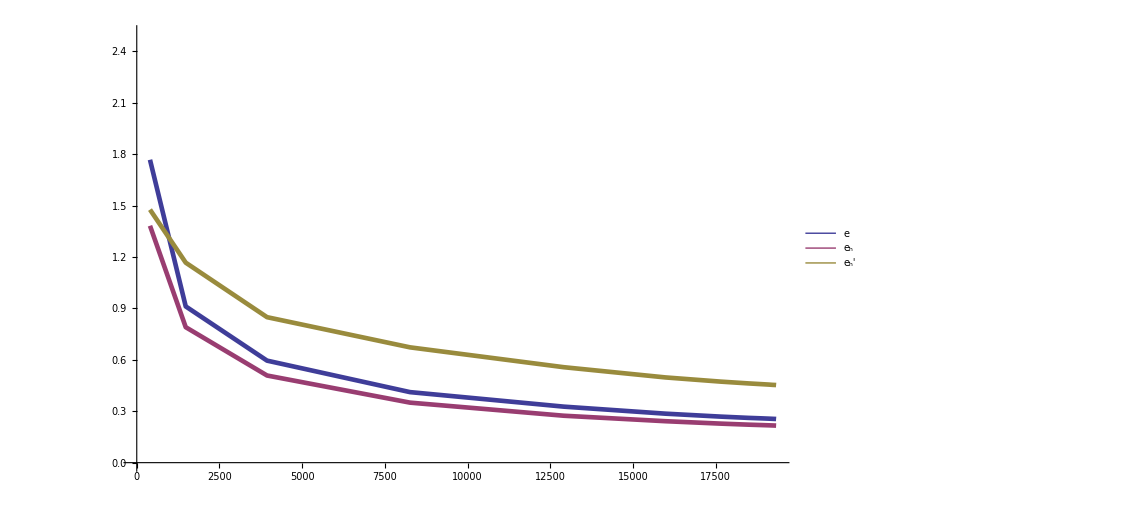

```mathematica
SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem1\\my\\errors\\"];
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];

ListLinePlot[{
	Transpose[{triangles, realErr}],
	Transpose[{triangles, myErr}],
	Transpose[{triangles, ostErr}]
},
PlotLegends->Placed[{
ToExpression["e",TeXForm,HoldForm],
ToExpression["e_h",TeXForm,HoldForm],
ToExpression["e_h^\prime",TeXForm,HoldForm]
},{0.8,.5}],
PlotRange -> {0,2.5},
BaseStyle->{FontSize->30},
PlotStyle->{Thickness->0.004,Thickness->0.004,Thickness->0.004}
]
```

```mathematica
,
```

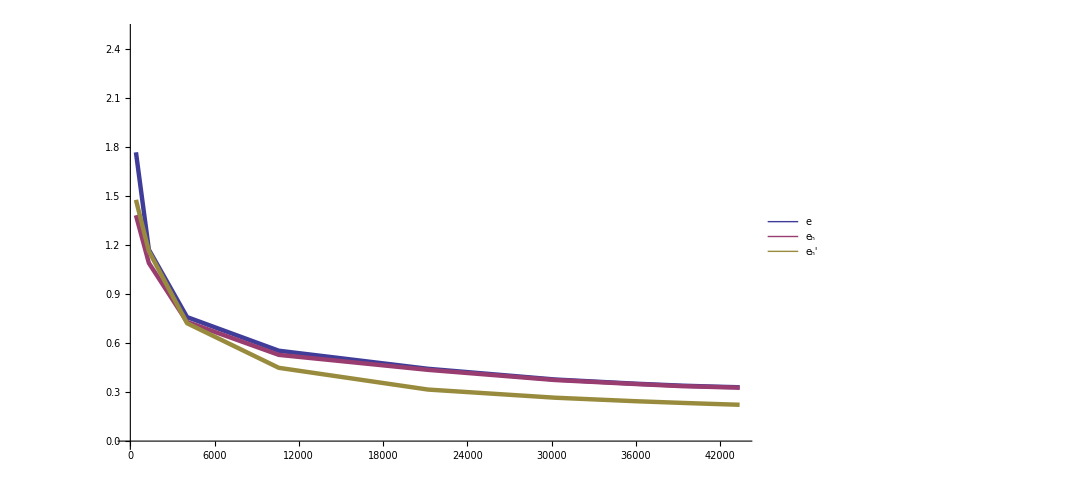

```mathematica
SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem1\\ost\\errors\\"];
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];

ListLinePlot[{
	Transpose[{triangles, realErr}],
	Transpose[{triangles, myErr}],
	Transpose[{triangles, ostErr}]
},
PlotLegends->Placed[{
ToExpression["e",TeXForm,HoldForm],
ToExpression["e_h",TeXForm,HoldForm],
ToExpression["e_h^\prime",TeXForm,HoldForm]
},{0.8,.5}],
BaseStyle->{FontSize->30},
PlotStyle->{Thickness->0.004,Thickness->0.004,Thickness->0.004},
PlotRange -> {0,2.5}]
```